# Halo Profile Equation Derivations

This notebook seeks to derive expressions for the halo density CDF (h), and fourier transform (p) for a number of halo profiles in halomod.

## Constant Density

```mathematica
f[x_]:=1.0
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}]//FullSimplify;{h[c],TeXForm[h[c]]}
```

{0.333333 c^3,0.333333 c^3}

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}]//FullSimplify;{p[k,c]//FullSimplify,TeXForm[p[k,c]]}
```

{(1. (-c k Cos[c k]+Sin[c k]))/k^3,\frac{1. (\sin (c k)-c k \cos (c k))}{k^3}}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{∫_0^∞ (1. x Sin[k x])/k ⅆx,\int_0^{\infty } \frac{1. x \sin (k x)}{k} \, dx}

## Number 1

```mathematica
f[x_]:= (2Pi)^(-3/2)*Exp[-x^2/2]
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}];{h[c],TeXForm[h[c]]}
```

{(-√2 c ⅇ^(-c^2/2)+√π Erf[c/(√2)])/(4 π^(3/2)),\frac{\sqrt{\pi } \text{erf}\left(\frac{c}{\sqrt{2}}\right)-\sqrt{2} c e^{-\frac{c^2}{2}}}{4 \pi ^{3/2}}}

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{(ⅇ^(1/2 (-c^2-2 ⅈ c k-k^2)) (2 ⅈ ⅇ^(k^2/2) (-1+ⅇ^(2 ⅈ c k))+ⅇ^(1/2 c (c+2 ⅈ k)) k √(2 π) (Erf[(c-ⅈ k)/(√2)]+Erf[(c+ⅈ k)/(√2)])))/(8 √2 k π^(3/2)),\frac{e^{\frac{1}{2} \left(-c^2-2 i c k-k^2\right)} \left(\sqrt{2 \pi } k e^{\frac{1}{2} c (c+2 i k)} \left(\text{erf}\left(\frac{c-i k}{\sqrt{2}}\right)+\text{erf}\left(\frac{c+i k}{\sqrt{2}}\right)\right)+2 i e^{\frac{k^2}{2}} \left(-1+e^{2 i c k}\right)\right)}{8 \sqrt{2} \pi ^{3/2} k}}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{(ⅇ^(-k^2/2))/(4 π),\frac{e^{-\frac{k^2}{2}}}{4 \pi }}

## Number 2

```mathematica
f[x_]:= Exp[-x]/(8*Pi)
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}]//FullSimplify;{h[c],TeXForm[h[c]]}
```

{(2-(2+c (2+c)) ⅇ^-c)/(8 π),\frac{2-(c (c+2)+2) e^{-c}}{8 \pi }}

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{(ⅇ^-c (2 ⅇ^c k-k (2+c+c k^2) Cos[c k]-(1+c+(-1+c) k^2) Sin[c k]))/(8 k (1+k^2)^2 π),\frac{e^{-c} \left(-\left((c-1) k^2+c+1\right) \sin (c k)-k \left(c k^2+c+2\right) \cos (c k)+2 e^c k\right)}{8 \pi  k \left(k^2+1\right)^2}}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{ConditionalExpression[1/(4 (1+k^2)^2 π),Abs[Im[k]]<1],\text{ConditionalExpression}\left[\frac{1}{4 \pi  \left(k^2+1\right)^2},\left| \Im(k)\right| <1\right]}

## Number 3

```mathematica
f[x_]:= Exp[-x]/(4*Pi*x^2)
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}];{h[c],TeXForm[h[c]]}
```

{(1-Cosh[c]+Sinh[c])/(4 π),\frac{\sinh (c)-\cosh (c)+1}{4 \pi }}

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{1/(16 k π)ⅈ (2 ExpIntegralEi[c (-1-ⅈ k)]-2 ExpIntegralEi[ⅈ c (ⅈ+k)]-Log[-1-ⅈ k]+Log[-1+ⅈ k]+Log[ⅈ/(-ⅈ+k)]-Log[-ⅈ/(ⅈ+k)]),\frac{i \left(2 \text{Ei}(c (-i k-1))-2 \text{Ei}(i c (k+i))-\log (-1-i k)+\log (-1+i k)+\log \left(\frac{i}{k-i}\right)-\log \left(-\frac{i}{k+i}\right)\right)}{16 \pi  k}}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{ConditionalExpression[ArcTan[k]/(4 k π),Abs[Im[k]]≤1],\text{ConditionalExpression}\left[\frac{\tan ^{-1}(k)}{4 \pi  k},\left| \Im(k)\right| \leq 1\right]}

## Number 4

```mathematica
f[x_]:=x^(-2)/(2 Pi^2*(1+x^2))
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}];{h[c],TeXForm[h[c]]}
```

{ConditionalExpression[ArcTan[c]/(2 π^2),Re[1/c]≠0||Im[1/c]>1||Im[1/c]<-1],\text{ConditionalExpression}\left[\frac{\tan ^{-1}(c)}{2 \pi ^2},\Re\left(\frac{1}{c}\right)\neq 0\lor \Im\left(\frac{1}{c}\right)>1\lor \Im\left(\frac{1}{c}\right)<-1\right]}

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{ConditionalExpression[1/(4 k π^2)(-ⅈ (CosIntegral[-(-ⅈ+c) k]-CosIntegral[(ⅈ+c) k]) Sinh[k]+2 SinIntegral[c k]+Cosh[k] (-SinIntegral[(ⅈ+c) k]+SinIntegral[ⅈ k-c k])),Im[c]==0&&Re[c]>0&&(Re[k]==0||(c Im[k]≤Re[k]&&Re[k]>0&&Re[c]≤Re[k]/Im[k])||(Re[k]>0&&k∈Reals)||(c+Re[k]/Im[k]≤0&&(Im[k]≤0||Re[k]≤0))||(Im[k]≤0&&(Re[k]≤0||Im[k]+Re[k]^2/Im[k]≤0)))],\text{ConditionalExpression}\left[\frac{-i \sinh (k) (\text{Ci}(-(c-i) k)-\text{Ci}((c+i) k))+2 \text{Si}(c k)+\cosh (k) (\text{Si}(i k-c k)-\text{Si}((c+i) k))}{4 \pi ^2 k},c=\Re(c)\land \Re(c)>0\land \left(\Re(k)=0\lor \left(c \Im(k)\leq \Re(k)\land \Re(k)>0\land c\leq \frac{\Re(k)}{\Im(k)}\right)\lor k>0\lor \left(c+\frac{\Re(k)}{\Im(k)}\leq 0\land (\Im(k)\leq 0\lor \Re(k)\leq 0)\right)\lor \left(\Im(k)\leq 0\land \left(\Re(k)\leq 0\lor \frac{k k^*}{\Im(k)}\leq 0\right)\right)\right)\right]}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{ConditionalExpression[(ⅇ^(-Abs[k]) (-1+ⅇ^Abs[k]) Sign[k])/(4 k π),k∈Reals],\text{ConditionalExpression}\left[\frac{e^{-\left| k\right| } \left(e^{\left| k\right| }-1\right) \text{sgn}(k)}{4 \pi  k},k\in \mathbb{R}\right]}

## Number 6

```mathematica
f[x_]:=1/(4 Pi d x^2)
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}];{h[c],TeXForm[h[c]]}
```

{c/(4 d π),\frac{c}{4 \pi  d}}

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{SinIntegral[c k]/(4 d k π),\frac{\text{Si}(c k)}{4 \pi  d k}}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{ConditionalExpression[Sign[k]/(8 d k),k∈Reals],\text{ConditionalExpression}\left[\frac{\text{sgn}(k)}{8 d k},k\in \mathbb{R}\right]}

## Hernquist

```mathematica
f[x_]:=x^(-1) /(1+x)^3
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}];{h[c],TeXForm[h[c]]}
```

{ConditionalExpression[c^2/(2 (1+c)^2),((Re[1/c]≥0||Re[1/c]≤-1)&&(c∉Reals||Re[1/c]<-1||Re[c]≥0))||1/c∉Reals],\text{ConditionalExpression}\left[\frac{c^2}{2 (c+1)^2},\left(\left(\Re\left(\frac{1}{c}\right)\geq 0\lor \Re\left(\frac{1}{c}\right)\leq -1\right)\land \left(c\notin \mathbb{R}\lor \Re\left(\frac{1}{c}\right)<-1\lor \Re(c)\geq 0\right)\right)\lor \frac{1}{c}\notin \mathbb{R}\right]}

```mathematica
TeXForm[FullSimplify[1/k(-1/2 k (-1+k CosIntegral[k] Sin[k]-k Cos[k] SinIntegral[k])+1/2 (-((1+c) k Cos[c k]+Sin[c k])/(1+c)^2+k^2 (CosIntegral[k+c k] Sin[k]-Cos[k] SinIntegral[k+c k])))]]
```

\frac{k^2 (\sin (k) (\text{Ci}(c k+k)-\text{Ci}(k))+\cos (k) (\text{Si}(k)-\text{Si}(c k+k)))-\frac{\sin (c k)+(c+1)
   k \cos (c k)}{(c+1)^2}+k}{2 k}

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{ConditionalExpression[1/k(-1/2 k (-1+k CosIntegral[k] Sin[k]-k Cos[k] SinIntegral[k])+1/2 (-((1+c) k Cos[c k]+Sin[c k])/(1+c)^2+k^2 (CosIntegral[k+c k] Sin[k]-Cos[k] SinIntegral[k+c k]))),(Im[k]/(Im[k] Re[c]+Im[c] Re[k])≤-1||(Im[k] Re[c]+Im[c] Re[k]≥0&&(Im[k]≥0||Im[c] (Im[k]^2+Re[k]^2)≥0))||(Im[k] Re[c]+Im[c] Re[k]≤0&&(Im[k]≤0||Im[c] (Im[k]^2+Re[k]^2)≤0)))&&(1/c∉Reals||Re[1/c]≥0||Re[1/c]≤-1)&&(1/c∉Reals||Re[1/c]<-1||c∉Reals||Re[c]≥0)],\text{ConditionalExpression}\left[\frac{\frac{1}{2} \left(k^2 (\sin (k) \text{Ci}(c k+k)-\cos (k) \text{Si}(c k+k))-\frac{\sin (c k)+(c+1) k \cos (c k)}{(c+1)^2}\right)-\frac{1}{2} k (k \text{Ci}(k) \sin (k)-k \text{Si}(k) \cos (k)-1)}{k},\left(\frac{\Im(k)}{\Re(c) \Im(k)+\Im(c) \Re(k)}\leq -1\lor \left(\Re(c) \Im(k)+\Im(c) \Re(k)\geq 0\land \left(\Im(k)\geq 0\lor \Im(c) \left(\Im(k)^2+\Re(k)^2\right)\geq 0\right)\right)\lor \left(\Re(c) \Im(k)+\Im(c) \Re(k)\leq 0\land \left(\Im(k)\leq 0\lor \Im(c) \left(\Im(k)^2+\Re(k)^2\right)\leq 0\right)\right)\right)\land \left(\frac{1}{c}\notin \mathbb{R}\lor \Re\left(\frac{1}{c}\right)\geq 0\lor \Re\left(\frac{1}{c}\right)\leq -1\right)\land \left(\frac{1}{c}\notin \mathbb{R}\lor \Re\left(\frac{1}{c}\right)<-1\lor c\notin \mathbb{R}\lor \Re(c)\geq 0\right)\right]}

```mathematica
N[SinIntegral[1]]
```

0.946083

```mathematica
-1+ CosIntegral[1] Sin[1]-Cos[1] SinIntegral[1]
```

-1+CosIntegral[1] Sin[1]-Cos[1] SinIntegral[1]

```mathematica
-((1+5)  Cos[5]+Sin[5])/(1+5)^2
```

1/36 (-6 Cos[5]-Sin[5])

```mathematica
N[1/36 (-6 Cos[5]-Sin[5])]
```

-0.0206402

```mathematica
N[-1+CosIntegral[1] Sin[1]-Cos[1] SinIntegral[1]]
```

-1.22726

```mathematica
N[(CosIntegral[6] Sin[1]-Cos[1] SinIntegral[6])]
```

-0.82703

```mathematica
N[p[1,5]]
```

0.189792

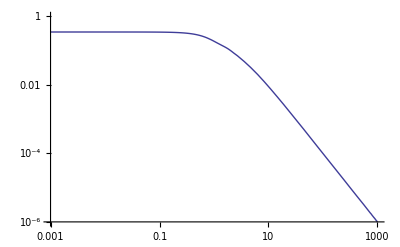

```mathematica
LogLogPlot[p[k,5.2],{k,10^-3,10^3}]
```

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{ConditionalExpression[1/4 (2-Abs[k] (π Cos[k]+2 CosIntegral[Abs[k]] Sin[Abs[k]])+2 k Cos[k] SinIntegral[k]),k∈Reals],\text{ConditionalExpression}\left[\frac{1}{4} (-\left| k\right|  (2 \text{Ci}(\left| k\right| ) \sin (\left| k\right| )+\pi  \cos (k))+2 k \text{Si}(k) \cos (k)+2),k\in \mathbb{R}\right]}

## Moore

```mathematica
f[x_]:=x^(-3/2) /(1+x^(3/2))
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}];{h[c],TeXForm[h[c]]}
```

{2/3 Log[1+c^(3/2)],\frac{2}{3} \log \left(c^{3/2}+1\right)}

```mathematica
Log[10]
```

Log[10]

```mathematica
N[Log[10]]
```

2.30259

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{∫_0^c Sin[k x]/(k √x (1+x^(3/2)))ⅆx,\int_0^c \frac{\sin (k x)}{k \sqrt{x} \left(x^{3/2}+1\right)} \, dx}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{ConditionalExpression[MeijerG[{{1/6,5/12,11/12},{}},{{1/6,1/6,5/12,1/2,2/3,5/6,11/12},{0,1/3}},k^6/46656]/(4 √3 π^(5/2) Abs[k]),k∈Reals],\text{ConditionalExpression}\left[\frac{G_{3,9}^{7,3}\left(\frac{k^6}{46656}|
\begin{array}{c}
 \frac{1}{6},\frac{5}{12},\frac{11}{12} \\
 \frac{1}{6},\frac{1}{6},\frac{5}{12},\frac{1}{2},\frac{2}{3},\frac{5}{6},\frac{11}{12},0,\frac{1}{3} \\
\end{array}
\right)}{4 \sqrt{3} \pi ^{5/2} \left| k\right| },k\in \mathbb{R}\right]}

## General NFW-like

```mathematica
f[x_]:=x^(-a) (1+x)^(a-3)
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}];{h[c],TeXForm[h[c]]}
```

{ConditionalExpression[-(-c)^a c^-a Beta[-c,3-a,-2+a],Re[a]<3&&(Re[1/c]≥0||Re[1/c]≤-1||1/c∉Reals)],\text{ConditionalExpression}\left[-(-c)^a c^{-a} B_{-c}(3-a,a-2),\Re(a)<3\land \left(\Re\left(\frac{1}{c}\right)\geq 0\lor \Re\left(\frac{1}{c}\right)\leq -1\lor \frac{1}{c}\notin \mathbb{R}\right)\right]}

```mathematica
a = 1.2; h[4.2]
```

0.94186

```mathematica
(-4.2)^1.2
```

-4.52748-3.28941 ⅈ

```mathematica
Beta[-4.2,2.8,-0.8]
```

-1.49264+1.08446 ⅈ

```mathematica
4.52748 * 1.49264 /4.2^1.2
```

1.20757

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{∫_0^c (x^(1-a) (1+x)^(-3+a) Sin[k x])/k ⅆx,\int_0^c \frac{x^{1-a} (x+1)^{a-3} \sin (k x)}{k} \, dx}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{ConditionalExpression[(2^-a MeijerG[{{1/2 (-2+a),1/2 (-1+a)},{}},{{0,0,1/2},{-1/2}},k^2/4])/(√π Gamma[3-a]),k∈Reals&&Re[a]<3],\text{ConditionalExpression}\left[\frac{2^{-a} G_{2,4}^{3,2}\left(\frac{k^2}{4}|
\begin{array}{c}
 \frac{a-2}{2},\frac{a-1}{2} \\
 0,0,\frac{1}{2},-\frac{1}{2} \\
\end{array}
\right)}{\sqrt{\pi } \Gamma (3-a)},k\in \mathbb{R}\land \Re(a)<3\right]}

## Very General NFW-like

```mathematica
f[x_]:=x^(-a) (1+x)^(a-b)
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}];{h[c],TeXForm[h[c]]}
```

{ConditionalExpression[-(-c)^a c^-a Beta[-c,3-a,1+a-b],Re[a]<3&&(Re[1/c]≥0||Re[1/c]≤-1||1/c∉Reals)],\text{ConditionalExpression}\left[-(-c)^a c^{-a} B_{-c}(3-a,a-b+1),\Re(a)<3\land \left(\Re\left(\frac{1}{c}\right)\geq 0\lor \Re\left(\frac{1}{c}\right)\leq -1\lor \frac{1}{c}\notin \mathbb{R}\right)\right]}

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{∫_0^c (x^(1-a) (1+x)^(a-b) Sin[k x])/k ⅆx,\int_0^c \frac{x^{1-a} (x+1)^{a-b} \sin (k x)}{k} \, dx}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{ConditionalExpression[(Abs[k]^3 Gamma[3-a] Gamma[-3+b] HypergeometricPFQ[{3/2-a/2,2-a/2},{3/2,2-b/2,5/2-b/2},-k^2/4]-Abs[k]^(1+b) Cos[(b π)/2] Gamma[1-b] Gamma[1-a+b] HypergeometricPFQ[{1/2-a/2+b/2,1-a/2+b/2},{3/2,1/2+b/2,b/2},-k^2/4]+Abs[k]^b Gamma[2-b] Gamma[-a+b] HypergeometricPFQ[{-a/2+b/2,1/2-a/2+b/2},{1/2,-1/2+b/2,b/2},-k^2/4] Sin[(b π)/2])/(k^2 Abs[k] Gamma[-a+b]),k∈Reals&&Re[a]<3&&Re[b]>1],\text{ConditionalExpression}\left[\frac{\Gamma (3-a) \left| k\right| ^3 \Gamma (b-3) \, _2F_3\left(\frac{3}{2}-\frac{a}{2},2-\frac{a}{2};\frac{3}{2},2-\frac{b}{2},\frac{5}{2}-\frac{b}{2};-\frac{k^2}{4}\right)-\cos \left(\frac{\pi  b}{2}\right) \Gamma (1-b) \Gamma (-a+b+1) \left| k\right| ^{b+1} \, _2F_3\left(-\frac{a}{2}+\frac{b}{2}+\frac{1}{2},-\frac{a}{2}+\frac{b}{2}+1;\frac{3}{2},\frac{b}{2}+\frac{1}{2},\frac{b}{2};-\frac{k^2}{4}\right)+\sin \left(\frac{\pi  b}{2}\right) \Gamma (2-b) \Gamma (b-a) \left| k\right| ^b \, _2F_3\left(\frac{b}{2}-\frac{a}{2},-\frac{a}{2}+\frac{b}{2}+\frac{1}{2};\frac{1}{2},\frac{b}{2}-\frac{1}{2},\frac{b}{2};-\frac{k^2}{4}\right)}{k^2 \left| k\right|  \Gamma (b-a)},k\in \mathbb{R}\land \Re(a)<3\land \Re(b)>1\right]}

## General Moore-like

```mathematica
f[x_]:=x^(-a)/ (1+x^(3-a))
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}];{h[c],TeXForm[h[c]]}
```

{∫_0^c x^(2-a)/(1+x^(3-a))ⅆx,\int_0^c \frac{x^{2-a}}{x^{3-a}+1} \, dx}

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{∫_0^c (x^(1-a) Sin[k x])/(k (1+x^(3-a)))ⅆx,\int_0^c \frac{x^{1-a} \sin (k x)}{k \left(x^{3-a}+1\right)} \, dx}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{∫_0^∞ (x^(1-a) Sin[k x])/(k (1+x^(3-a)))ⅆx,\int_0^{\infty } \frac{x^{1-a} \sin (k x)}{k \left(x^{3-a}+1\right)} \, dx}

## NFW

```mathematica
f[x_]:=x^(-1) (1+x)^(1-3)
```

```mathematica
h[c_]:= Integrate[x^2 f[x],{x,0,c}];{h[c],TeXForm[h[c]]}
```

{ConditionalExpression[-1+1/(1+c)+Log[1+c],((Re[1/c]≥0||Re[1/c]≤-1)&&(c∉Reals||Re[1/c]<-1||Re[c]≥0))||1/c∉Reals],\text{ConditionalExpression}\left[\frac{1}{c+1}+\log (c+1)-1,\left(\left(\Re\left(\frac{1}{c}\right)\geq 0\lor \Re\left(\frac{1}{c}\right)\leq -1\right)\land \left(c\notin \mathbb{R}\lor \Re\left(\frac{1}{c}\right)<-1\lor \Re(c)\geq 0\right)\right)\lor \frac{1}{c}\notin \mathbb{R}\right]}

```mathematica
TeXForm[FullSimplify[1/k(-k (Cos[k] CosIntegral[k]+Sin[k] SinIntegral[k])+1/(1+c)((1+c) k Cos[k] CosIntegral[k+c k]-Sin[c k]+(1+c) k Sin[k] SinIntegral[k+c k]))]]
```

\cos (k) (\text{Ci}(c k+k)-\text{Ci}(k))+\sin (k) (\text{Si}(c k+k)-\text{Si}(k))-\frac{\sin (c k)}{c k+k}

```mathematica
p[k_,c_]:=Integrate[x Sin[k x]/k f[x],{x,0,c}];{p[k,c],TeXForm[p[k,c]]}
```

{ConditionalExpression[1/k(-k (Cos[k] CosIntegral[k]+Sin[k] SinIntegral[k])+1/(1+c)((1+c) k Cos[k] CosIntegral[k+c k]-Sin[c k]+(1+c) k Sin[k] SinIntegral[k+c k])),(Im[k]/(Im[k] Re[c]+Im[c] Re[k])≤-1||(Im[k] Re[c]+Im[c] Re[k]≥0&&(Im[k]≥0||Im[c] (Im[k]^2+Re[k]^2)≥0))||(Im[k] Re[c]+Im[c] Re[k]≤0&&(Im[k]≤0||Im[c] (Im[k]^2+Re[k]^2)≤0)))&&(1/c∉Reals||Re[1/c]≥0||Re[1/c]≤-1)&&(1/c∉Reals||Re[1/c]<-1||c∉Reals||Re[c]≥0)],\text{ConditionalExpression}\left[\frac{\frac{(c+1) k \cos (k) \text{Ci}(c k+k)+(c+1) k \sin (k) \text{Si}(c k+k)-\sin (c k)}{c+1}-k (\text{Ci}(k) \cos (k)+\text{Si}(k) \sin (k))}{k},\left(\frac{\Im(k)}{\Re(c) \Im(k)+\Im(c) \Re(k)}\leq -1\lor \left(\Re(c) \Im(k)+\Im(c) \Re(k)\geq 0\land \left(\Im(k)\geq 0\lor \Im(c) \left(\Im(k)^2+\Re(k)^2\right)\geq 0\right)\right)\lor \left(\Re(c) \Im(k)+\Im(c) \Re(k)\leq 0\land \left(\Im(k)\leq 0\lor \Im(c) \left(\Im(k)^2+\Re(k)^2\right)\leq 0\right)\right)\right)\land \left(\frac{1}{c}\notin \mathbb{R}\lor \Re\left(\frac{1}{c}\right)\geq 0\lor \Re\left(\frac{1}{c}\right)\leq -1\right)\land \left(\frac{1}{c}\notin \mathbb{R}\lor \Re\left(\frac{1}{c}\right)<-1\lor c\notin \mathbb{R}\lor \Re(c)\geq 0\right)\right]}

```mathematica
p[k_]:=Integrate[x Sin[k x]/k f[x],{x,0,Infinity}];{p[k],TeXForm[p[k]]}
```

{ConditionalExpression[1/2 ((π-2 Abs[k]) sin(Abs[k])-2 cos(k) Abs[k]),k∈ℝ],\text{ConditionalExpression}\left[\frac{1}{2} (\sin (\left| k\right| ) (\pi -2 \text{Si}(\left| k\right| ))-2 \cos (k) \text{Ci}(\left| k\right| )),k\in \mathbb{R}\right]}

```mathematica
f[x] = Integrate[]
```

```mathematica
D[Integrate[f[x],{x,y,Infinity}]]
```